## Символни преобразования

```mathematica
Expand[(x-1)^2] (*Представяне на полином в нормален вид*)
```

1-2 x+x^2

```mathematica
Expand[Sin[x^2] Cos[2x]]
```

Cos[2 x] Sin[x^2]

```mathematica
TrigExpand[Sin[x^2] Cos[2x]] (*За тригонометрични преобразования*)
```

```mathematica
Factor[%] (*Разлагане на полином*)
```

(-1+x)^2

```mathematica
Cancel[(x^2-1)/(x-1)]
```

1+x

Simplify и FullSimplify се стремят да представят даден израз във “възможно най-прост вид”.

```mathematica
Simplify[1-2x+x^2]
```

(-1+x)^2

```mathematica
Simplify[%]
```

(-1+x)^2

```mathematica
Simplify[1/4(1/(-1+x)-1/(1+x)-2/(1+x^2))]
```

1/(-1+x^4)

```mathematica
FullSimplify[1/4(1/(-1+x)-1/(1+x)-2/(1+x^2))]
```

1/(-1+x^4)

Принципът на действие на двете функции е да раздели подадения израз на части, върху които да приложи всички възможни правила за трансформация и да открие тази комбинация между отделните опростявания, която дава възможно “най-прост” резултат.
Разликата между двете е, че FullSimplify пробва по-голям набор от възможни трансформации. Например Simplify не може да се справи с изрази, съдържащи специални функции:

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

В някои случаи опростявания могат да се направят само при определени предположения. В такъв случай, е полезно да се използва фунцкията Refine. Нейното предимство пред Simplify и FullSimplify е, че е значително по-бърза, тъй като прави опростяване на база на директно заместване на числови стойности, отговарящи на съответното предположение, вместо да изпробва различни комбинации от правила за трансформация. Тя обаче невинаги може да се справи с опростяването:

```mathematica
Simplify[Sqrt[x^2]]
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],x>0]
```

x

```mathematica
Refine[Sqrt[x^2],x>0]
```

x

```mathematica
Simplify[Sqrt[x^2+2 x y+y^2],x+y≥0]
```

x+y

```mathematica
Refine[Sqrt[x^2+2 x y+y^2],x+y≥0]
```

√(x^2+2 x y+y^2)

### Действия с рационални функции

```mathematica
Together[a/b+c/d] (*Привеждане под общ знаменател*)
```

(b c+a d)/(b d)

```mathematica
Apart[%]
```

a/b+c/d

```mathematica
Cancel[(x^2-1)/(x-1)]
```

1+x

```mathematica
(*ExpandNumerator, ExpandDenominator...*)
```

## Комплексна аритметика

```mathematica
ⅈ^2 (* Esc + ii + Esc *)
```

-1

```mathematica
I^2
```

-1

```mathematica
complexNumber=3+2ⅈ
```

3+2 ⅈ

```mathematica
Re[complexNumber]
```

3

```mathematica
Im[complexNumber]
```

2

```mathematica
Abs[complexNumber]
```

√13

```mathematica
Conjugate[complexNumber]
```

3-2 ⅈ

## Целочислена аритметика

### Делимост

```mathematica
Mod[17,2] (*Остатък при деление на две числа*)
```

1.3

```mathematica
Quotient[17,5](*Частно*)
```

3

```mathematica
QuotientRemainder[17,5] (*Частно и остатък*)
```

{3,2}

```mathematica
Divisible[17,2](*Връща резултат True/False в зависимост от това дали второто число е делител на първото*)
```

False

```mathematica
Divisors[17] (*Пресмята делителите на дадено цяло число*)
```

{1,17}

```mathematica
GCD[2,3,5](*Най-голям общ делител*)
```

1

```mathematica
LCM[2,3,5](*Най-малко общо кратно*)
```

30

## Действия с полиноми

```mathematica
PolynomialQuotient[x^2,x+a,x]
```

-a+x

```mathematica
PolynomialRemainder[x^2,x+a,x]
```

a^2

```mathematica
PolynomialQuotientRemainder[x^2,x+a,x]
```

{-a+x,a^2}

```mathematica
(*PolynomialGCD, PolynomialLCM, CoefficientList[5 x^2+3x-5,x], Exponent*)
```

## Графики на функции на една променлива

### Plot Options

#### PlotRange

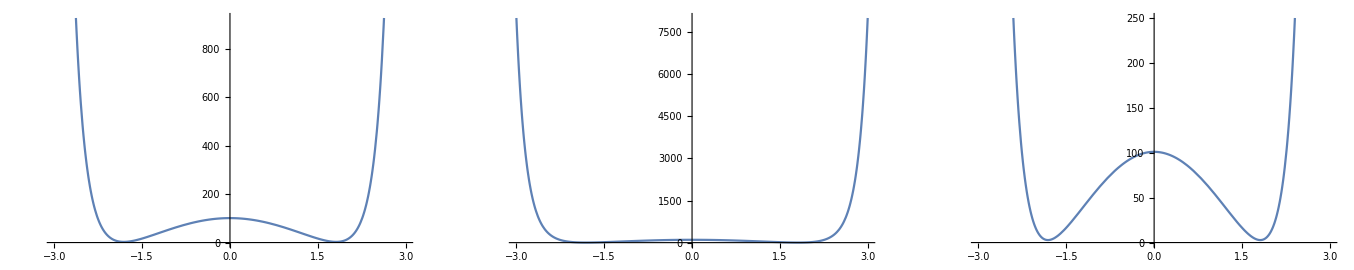

```mathematica
f[x_]:=100Cos[x]+E^(x^2)
GraphicsRow[
{Plot[f[x],{x,-3,3}],
Plot[f[x],{x,-3,3},PlotRange->All], 
Plot[f[x],{x,-3,3},PlotRange->{0,250}]}]
```

#### AspectRatio

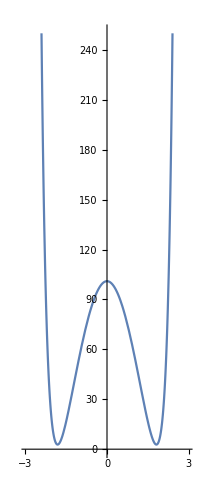

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{0,250}, AspectRatio->Automatic] (*Ratio of height to width is not looking good in this case, beacuse the function value rapidly gets larger*)
```

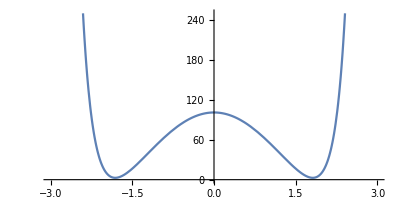

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{0,250}, AspectRatio->1/2]
```

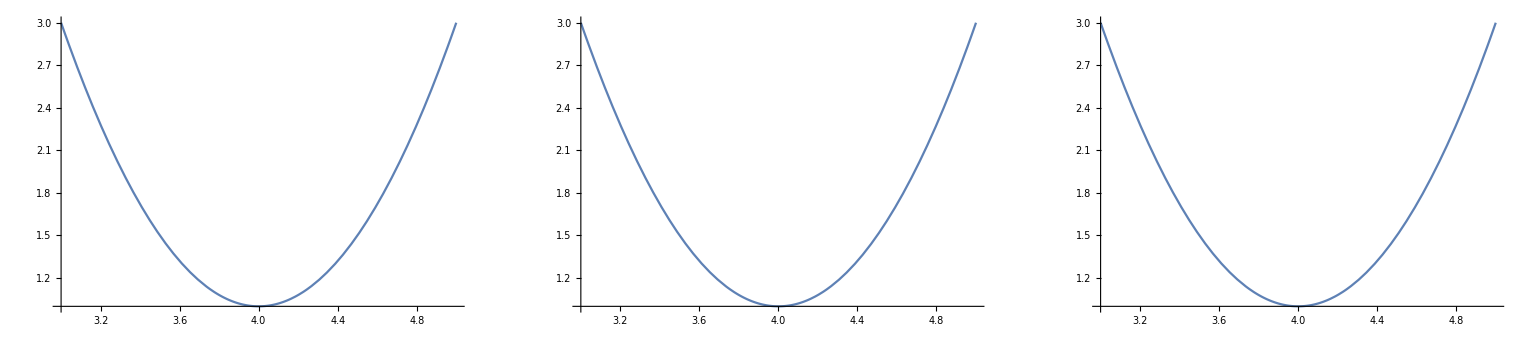

```mathematica
GraphicsRow[{Plot[2(x-4)^2+1,{x,3,5}],
Plot[2(x-4)^2+1,{x,3,5},AspectRatio->Automatic],
Plot[2(x-4)^2+1,{x,3,5},AspectRatio->0.5]}]
```

#### AxesOrigin

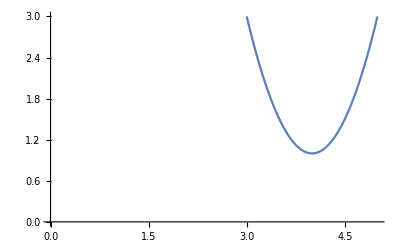

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesOrigin->{0,0}]
```

#### PlotStyle

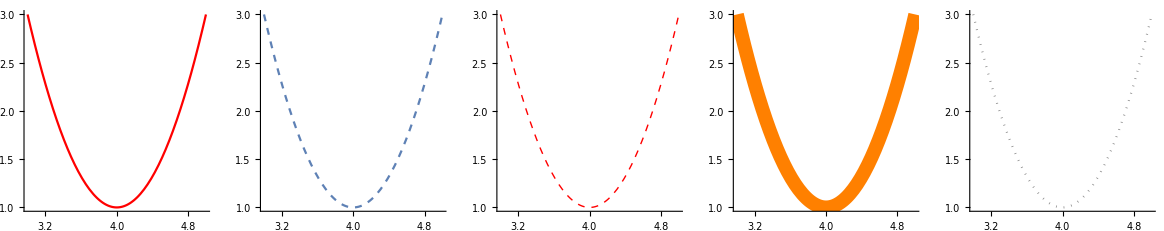

```mathematica
GraphicsRow[{Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Red],
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Dashed],
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Dashed,Red,Thick]],
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Orange,Thickness[0.025]]],
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Dotted,Gray]]}
]
```

## Визуализация на списъци от данни

```mathematica
data=Table[{k,Sin[3k]/5},{k,0,1,0.1}]
```

{{0.,0.},{0.1,0.059104},{0.2,0.112928},{0.3,0.156665},{0.4,0.186408},{0.5,0.199499},{0.6,0.19477},{0.7,0.172642},{0.8,0.135093},{0.9,0.085476},{1.,0.028224}}

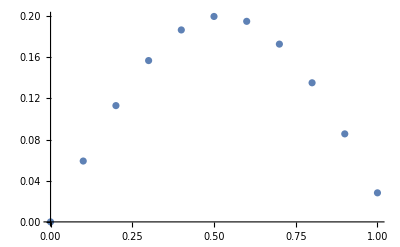

```mathematica
p1=ListPlot[data]
```

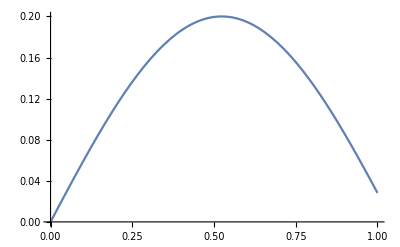

```mathematica
p2=Plot[Sin[3x]/5,{x,0,1},PlotRange->All]
```

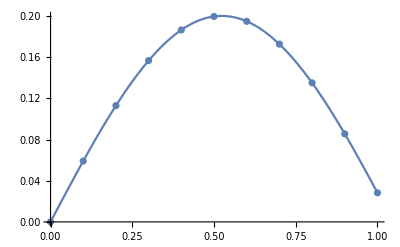

```mathematica
Show[p1,p2]
```